## Solution of Laplace’s equation on a semi-infinite strip

Solve ∇^2 u=0 on the semi-infinite strip  0<= x <= 1, y>= 0 with boundary conditions

u(x,0)=U_0(x)
u(0,y)=u(1,y)=0
u(x,y)-> 0 as y->∞.

With these BCs, the solution is

u(x,y)= Σ_(n=1)^∞ c_n v_n(x)e^-k_ny

where k_n=n π and v_n(x)=sin(k_n x). The coefficients c_n are obtained by orthogonal projection,

c_n=⟨v_n,U_0⟩/⟨v_n,v_n⟩

with the inner product

⟨f,g⟩=∫_0^1 f(x)g(x)ⅆx.

### Set up

#### Define the inner product to use

```mathematica
IP[u_,v_]:=Integrate[u v, {x,0,1}]
```

Be sure to use deferred assignment here (“:=” instead of “=”)

#### Define the eigenfunctions

```mathematica
Subscript[k, n_]=n Pi
```

π n

```mathematica
Subscript[v, n_][x_]=Sin[Subscript[k, n] x]
```

sin(π n x)

## Example 1

In this example, the boundary value at y=0 is U_0(x)=sin(π x)+3/4 sin(2 π x)+1/5 sin(3 π x). This function is already written explicitly as a sum of eigenfunctions,

U_0(x)=v_1(x)+3/4 v_2(x)+1/5 v_3(x)

so the solution will be

u(x,y)=sin(π x)e^(-π y)+3/4 sin(2π x)e^(-2π y)+1/5 sin(3 π x)e^(-3π y).

#### Define the function value at the non-homogeneous boundary

```mathematica
Subscript[U, 0][x_]=Subscript[v, 1][x]+3/4 Subscript[v, 2][x]+1/5 Subscript[v, 3][x]
```

sin(π x)+3/4 sin(2 π x)+1/5 sin(3 π x)

Show the function

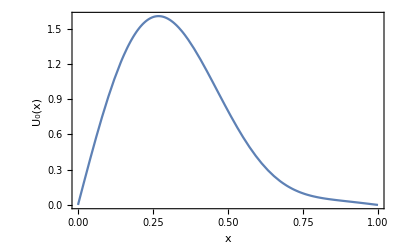

```mathematica
Plot[Subscript[U, 0][x],{x,0,1},FrameLabel->{x,"U_0(x)"}]
```

#### Compute the coefficients

We’ll need to do some integrals. While Mathematica can do all the integrals easily, you’ll need to be careful: in some problems the result might come out in a form that’s difficult to use directly. This example is such a problem.

Do the integrals:

```mathematica
Subscript[c, n_]=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

-((n^4-10 n^2+249) sin(π n))/(10 π (n^2 (n^2-7)^2-36) (1/2-(sin(2 π n))/(4 π n)))

Notice the sin(n π) in the numerator: the numerator is zero whenever n is an integer.Let’s look at the denominator:

```mathematica
Factor[Denominator[Subscript[c, n]]]
```

(5 (n-3) (n-2) (n-1) (n+1) (n+2) (n+3) (2 π n-sin(2 π n)))/(2 n)

The denominator is zero for n=1,2,3, nonzero for all other natural numbers. At n=1,2,3 the expression for the coefficients is indeterminate.

```mathematica
Factor[Subscript[c, n]]
```

-(2 n (n^4-10 n^2+249) sin(π n))/(5 (n-3) (n-2) (n-1) (n+1) (n+2) (n+3) (2 π n-sin(2 π n)))

You can resolve the indeterminacy with L’Hopital’s rule, for example

```mathematica
Limit[Subscript[c, n],n->3]
```

1/5

but it’s usually simpler to just use deferred evaluation

```mathematica
Subscript[c, n_]:=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

This way, the integral isn’t evaluated until the value of n is known, at which point Mathematica can do an integral specialized to that value.

Let’s see a few values:

```mathematica
Table[{n,Subscript[c, n]},{n,1,5}]
```

(1 | 1
2 | 3/4
3 | 1/5
4 | 0
5 | 0)

#### Form the solution to Laplace’s equation

Write a function to add up the first M terms in the partial sums.

```mathematica
uSum[M_,x_,y_]:=Sum[Subscript[c, n] Subscript[v, n][x]Exp[-Subscript[k, n]y],{n,1,M}]
```

In this case, we need only 3 terms.

```mathematica
u3[x_,y_]=uSum[3,x,y]
```

ⅇ^(-π y) sin(π x)+3/4 ⅇ^(-2 π y) sin(2 π x)+1/5 ⅇ^(-3 π y) sin(3 π x)

That’s the solution we worked out by hand.

#### Plot the solution

The problem is posed on a semi-infinite strip so we can’t plot the whole domain. The slowest decaying term goes as e^(-π y), which will decrease to e^-π≈0.043 at y=1 and e^(-3π/2)≈0.009 at y=3/2. Since 1% accuracy is good enough for a rough plot, we’ll plot y∈[0,3/2] instead of y∈[0,∞].

Here’s a 3D plot. The “ZMesh” option shows the contour levels on the surface. I chose the ViewPoint to show the shape nicely. You can use the mouse to rotate the image and see it from different angles.

```mathematica
Plot3D[u3[x,y],{x,0,1},{y,0,3/2},PlotRange->All, PlotTheme->"ZMesh",ViewPoint->{1.3,2.4,2}]
```

-Graphics3D-

## Example 2

#### Define the function value at the non-homogeneous boundary

```mathematica
Subscript[U, 0][x_]=Piecewise[{{2x,x<1/2},{2(1-x),x>=1/2}}]
```

Piecewise[{{2 x, x<1/2}, {2 (1-x), x≥1/2}}]

Show the function

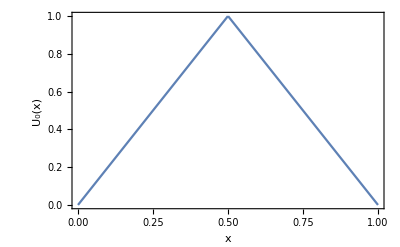

```mathematica
Plot[Subscript[U, 0][x],{x,0,1},FrameLabel->{x,"U_0(x)"}]
```

#### Compute the coefficients

In this case, we’ll be ok without deferred evaluation

```mathematica
Subscript[c, n_]=IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]
```

(2 (2 sin((π n)/2)-sin(π n)))/(π^2 n^2 (1/2-(sin(2 π n))/(4 π n)))

It can be cleaned up a bit by specifying that n is an integer

```mathematica
Subscript[c, n_]=Assuming[n∈ Integers,IP[Subscript[v, n][x],Subscript[U, 0][x]]/IP[Subscript[v, n][x],Subscript[v, n][x]]]
```

(8 sin((π n)/2))/(π^2 n^2)

Show a few:

```mathematica
Table[{n,Subscript[c, n]},{n,1,5}]
```

(1 | 8/π^2
2 | 0
3 | -8/(9 π^2)
4 | 0
5 | 8/(25 π^2))

#### Form the solution to Laplace’s equation

Write a function to add up the first M terms in the partial sums.

```mathematica
uSum[M_,x_,y_]:=Sum[Subscript[c, n] Subscript[v, n][x]Exp[-Subscript[k, n]y],{n,1,M}]
```

Show a sum with a few terms

```mathematica
u7[x_,y_]=uSum[7,x,y]
```

(8 ⅇ^(-π y) sin(π x))/π^2-(8 ⅇ^(-3 π y) sin(3 π x))/(9 π^2)+(8 ⅇ^(-5 π y) sin(5 π x))/(25 π^2)-(8 ⅇ^(-7 π y) sin(7 π x))/(49 π^2)

To see how many terms are needed, let’s plot the value at y=0.

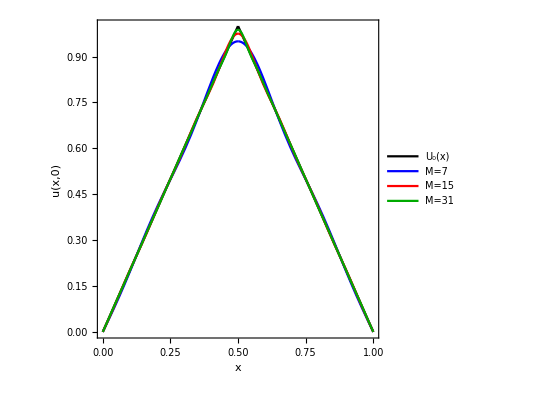

```mathematica
Plot[{Subscript[U, 0][x],uSum[7,x,0],uSum[15,x,0], uSum[31, x, 0]},{x,0,1},FrameLabel->{x,"u(x,0)"},AspectRatio->1,PlotStyle->{Black,Blue,Red,Darker[Green]},PlotLegends->Placed[{"U_0(x)", "M=7", "M=15", "M=31"},Right]]
```

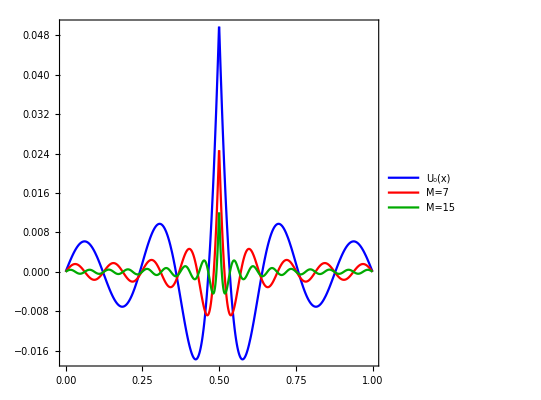

```mathematica
Plot[{Subscript[U, 0][x]-uSum[7,x,0],Subscript[U, 0][x]-uSum[15,x,0], Subscript[U, 0][x]-uSum[31, x, 0]},{x,0,1},PlotRange->All,AspectRatio->1,PlotStyle->{Blue,Red,Darker[Green]},PlotLegends->Placed[{"U_0(x)", "M=7", "M=15", "M=31"},Right]]
```

With 31 terms we get to just over 1% accuracy, so let’s use that.

```mathematica
u31[x_,y_]=uSum[31, x, y]
```

(8 ⅇ^(-π y) sin(π x))/π^2-(8 ⅇ^(-3 π y) sin(3 π x))/(9 π^2)+(8 ⅇ^(-5 π y) sin(5 π x))/(25 π^2)-(8 ⅇ^(-7 π y) sin(7 π x))/(49 π^2)+(8 ⅇ^(-9 π y) sin(9 π x))/(81 π^2)-(8 ⅇ^(-11 π y) sin(11 π x))/(121 π^2)+(8 ⅇ^(-13 π y) sin(13 π x))/(169 π^2)-(8 ⅇ^(-15 π y) sin(15 π x))/(225 π^2)+(8 ⅇ^(-17 π y) sin(17 π x))/(289 π^2)-(8 ⅇ^(-19 π y) sin(19 π x))/(361 π^2)+(8 ⅇ^(-21 π y) sin(21 π x))/(441 π^2)-(8 ⅇ^(-23 π y) sin(23 π x))/(529 π^2)+(8 ⅇ^(-25 π y) sin(25 π x))/(625 π^2)-(8 ⅇ^(-27 π y) sin(27 π x))/(729 π^2)+(8 ⅇ^(-29 π y) sin(29 π x))/(841 π^2)-(8 ⅇ^(-31 π y) sin(31 π x))/(961 π^2)

#### Plot the solution

```mathematica
Plot3D[u31[x,y],{x,0,1},{y,0,3/2},PlotRange->All, PlotTheme->"ZMesh",ViewPoint->{1.3,2.4,2}]
```

-Graphics3D-